# 4.2 a)

Calculate radius if limit cycle by setting r’ =0   which gives  0=mu*r-r^3 => r^2=mu => r=0 or r=sqrt(mu) or r= -sqrt(mu)
Calcualte periopd T: periodtime = 2 pi/phi’    and phi’ = omega + nu *r^2 
therfore T= 2 Pi /(omega + nu * mu)

# 4.2 b)

```mathematica
ClearAll["Global`*"]

leftDerivative1=D[Sqrt[x1[t]^2+x2[t]^2],t]//Simplify;
leftDerivative2=D[ArcTan[x1[t],x2[t]],t]//Simplify;


rightHandSide1=(Sqrt[x1[t]^2+x2[t]^2])*(μ-(x1[t]^2+x2[t]^2));
rightHandSide2=ω+ν*(x1[t]^2+x2[t]^2);

equation1=leftDerivative1==rightHandSide1;
equation2=leftDerivative2==rightHandSide2;
solution1=Solve[equation1,x1'[t]]//Simplify;
solution2=Solve[equation2,x2'[t]]//Simplify;
solution2WithSubstitution=solution2/. solution1[[1]]//Simplify;


derivativeEquation1=x2'[t]==ν x1[t]^3+x1[t] (ω+2 ν x2[t]^2)+(x2[t] (-x1[t]^3+ω x2[t]+ν x2[t]^3+x1[t] (μ-2 x2[t]^2)-(x2[t] (-μ x2[t]+x2[t]^3+Derivative[1][x2][t]))/x1[t]))/x1[t];

solutionDerivative1=Solve[derivativeEquation1,x2'[t]]//ExpandAll;

solution1WithSubstitution=solution1/. solutionDerivative1[[1]]//ExpandAll
```

{{x1'[t]→μ x1[t]-x1[t]^3-ω x2[t]-ν x1[t]^2 x2[t]-x1[t] x2[t]^2-ν x2[t]^3}}

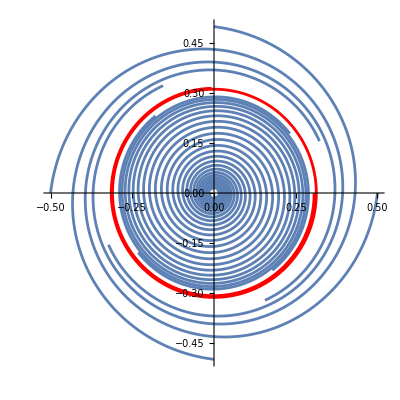

```mathematica
ClearAll["Global`*"]


muValue=1/10;
nuValue=1;
omegaValue=1;
eqX1=x1'[t]==muValue*x1[t]+nuValue*x1[t]^2*x2[t]-x1[t]*x2[t]^2-x1[t]^3+nuValue*x2[t]^3+omegaValue*x2[t];
eqX2=x2'[t]==-nuValue*x1[t]^3-nuValue*x1[t]*x2[t]^2-x1[t]^2*x2[t]-omegaValue*x1[t]+muValue*x2[t]-x2[t]^3;

system1={eqX1,eqX2};
fixedPoint1={0,0};

initialTime=0;
timeMax1=40;
timeMax2=5;
timeMax3=10;

distance1=0.01;
distance2=0.5;
distance3=Sqrt[muValue]-0.01;

initialConditions1={{x1[0]==fixedPoint1[[1]]+distance1,x2[0]==fixedPoint1[[2]]+distance1},{x1[0]==fixedPoint1[[1]]-distance1,x2[0]==fixedPoint1[[2]]+distance1},{x1[0]==fixedPoint1[[1]]+distance1,x2[0]==fixedPoint1[[2]]-distance1},{x1[0]==fixedPoint1[[1]]-distance1,x2[0]==fixedPoint1[[2]]-distance1}};

initialConditions2={{x1[0]==fixedPoint1[[1]]+distance2,x2[0]==fixedPoint1[[2]]},{x1[0]==fixedPoint1[[1]]-distance2,x2[0]==fixedPoint1[[2]]},{x1[0]==fixedPoint1[[1]],x2[0]==fixedPoint1[[2]]+distance2},{x1[0]==fixedPoint1[[1]],x2[0]==fixedPoint1[[2]]-distance2}};

initialConditionsLimitCycle={x1[0]==fixedPoint1[[1]]+distance3,x2[0]==fixedPoint1[[2]]};

sol1=NDSolve[{system1,#},{x1,x2},{t,initialTime,timeMax1}]&/@initialConditions1;
sol2=NDSolve[{system1,#},{x1,x2},{t,initialTime,timeMax2}]&/@initialConditions2;
sol3=NDSolve[{system1,initialConditionsLimitCycle},{x1,x2},{t,initialTime,timeMax3}];


plot1=ParametricPlot[Evaluate[{x1[t],x2[t]}/. #],{t,initialTime,timeMax1}]&/@sol1;
plot2=ParametricPlot[Evaluate[{x1[t],x2[t]}/. #],{t,initialTime,timeMax2}]&/@sol2;
plot3=ParametricPlot[Evaluate[{x1[t],x2[t]}/. sol3],{t,initialTime,timeMax3},PlotStyle->Red];

Show[plot1,plot2,plot3,FrameLabel->{"t","Solution"},PlotRange->Full]
```

# 4.2 c)

from b  [1/10,1,1]

# 4.2 d)

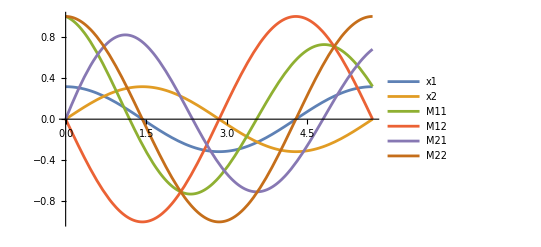

```mathematica
ClearAll["Global`*"]

(*Parameters*)
muValue=1/10;
omegaValue=1;
nuValue=1;

(*Define functions*)
f1[x1_,x2_]:=muValue*x1[t]-nuValue*x1[t]^2*x2[t]-x1[t]*x2[t]^2-x1[t]^3-nuValue*x2[t]^3-omegaValue*x2[t];
f2[x1_,x2_]:=nuValue*x1[t]^3+nuValue*x1[t]*x2[t]^2-x1[t]^2*x2[t]+omegaValue*x1[t]+muValue*x2[t]-x2[t]^3;

(*Calculate partial derivatives*)
J11=D[f1[x1,x2],x1[t]];
J12=D[f1[x1,x2],x2[t]];
J21=D[f2[x1,x2],x1[t]];
J22=D[f2[x1,x2],x2[t]];

(*Define system of differential equations*)
eqM11=M11'[t]==J11*M11[t]+J12*M21[t];
eqM12=M12'[t]==J11*M12[t]+J12*M22[t];
eqM21=M21'[t]==J21*M11[t]+J22*M21[t];
eqM22=M22'[t]==J21*M12[t]+J22*M22[t];

eqx1=x1'[t]==muValue*x1[t]-nuValue*x1[t]^2*x2[t]-x1[t]*x2[t]^2-x1[t]^3-nuValue*x2[t]^3-omegaValue*x2[t];
eqx2=x2'[t]==nuValue*x1[t]^3+nuValue*x1[t]*x2[t]^2-x1[t]^2*x2[t]+omegaValue*x1[t]+muValue*x2[t]-x2[t]^3;

system={eqM11,eqM12,eqM21,eqM22,eqx1,eqx2};
initialConditions={x1[0]==Sqrt[muValue],x2[0]==0,M11[0]==1,M12[0]==0,M21[0]==0,M22[0]==1};


initialTime=0;
timeMax=2*Pi/(omegaValue+nuValue*muValue);

sol=NDSolve[{system,initialConditions},{x1,x2,M11,M12,M21,M22},{t,initialTime,timeMax}];

{x1Values,x2Values,M11Values,M12Values,M21Values,M22Values}={x1[t],x2[t],M11[t],M12[t],M21[t],M22[t]}/. sol[[1]];

(*Plot the trajectories*)
plotTrajectories=Plot[Evaluate[{x1[t],x2[t],M11[t],M12[t],M21[t],M22[t]}/. sol[[1]]],{t,initialTime,timeMax},PlotLegends->{"x1","x2","M11","M12","M21","M22"},FrameLabel->{{"Values",None},{"Time","Trajectories of x1, x2, M11, M12, M21, M22"}},PlotRange->All];

Show[plotTrajectories]
```

# 4.2 e)

```mathematica
M11TMax=M11Values/. t->timeMax;
M12TMax=M12Values/. t->timeMax;
M21TMax=M21Values/. t->timeMax;
M22TMax=M22Values/. t->timeMax;


resultMatrix=Round[{{M11TMax,M12TMax},{M21TMax,M22TMax}},0.01]//MatrixForm
```

(0.32 | 0.
0.68 | 1.)

# 4.2 f)

```mathematica
solMat={{M11TMax,M12TMax},{M21TMax,M22TMax}};

eigenValues=Eigenvalues[solMat];

solTilde=Round[{1/timeMax*Log[eigenValues[[2]]],1/timeMax*Log[eigenValues[[1]]]},0.01]
```

{-0.2,0.}

# 4.2 g)

```mathematica
ClearAll["Global`*"]

J11=D[Sqrt[x1^2+x2^2],x1];
J12=D[Sqrt[x1^2+x2^2],x2];
J21=D[ArcTan[x1,x2],x1];
J22=D[ArcTan[x1,x2],x2];

JG={{J11,J12},{J21,J22}};
JGInv=Inverse[JG];

JakobiPol={{μ-3*r^2,0},{2*ν*r,0}};
JakExp=MatrixExp[JakobiPol*T];
T=2*Pi/(ω+ν*μ);
x1=Sqrt[μ];
x2=0;
ω=1;
ν=1;
μ=1/10;
r=Sqrt[x1^2+x2^2];

solM=JGInv.JakExp.JG//Simplify
```

{{ⅇ^(-4 π/11),0},{1-ⅇ^(-4 π/11),1}}

# 4.2 h)

```mathematica
solm = Eigenvalues[solM];

Round[{1/T * Log[solm[[2]]],1/T * Log[solm[[1]]]},0.1]
```

{-0.2,0.}